We want to quantify the relationship between the allowed precision of the solution and the divergence of the two mathematica builds: generated and extracted coefficients

First we define the precision and other variables . Precision in mathematica is the effective number of digits of precision, so if precision is a then x should be precise to 10^(-a)
By decreasing precision ϵ  “epsi1” and δ  “delt1” users can identify parameter ranges where this implementation can no longer find an acceptable set of coefficients.,

```mathematica
P=15;
delt1=0.3;
alph1=1;
epsi1=10^(-6);
```

```mathematica
myN[x_]:=N[x];
myP[x_]:=SetPrecision[x, P];
```

flt20 with varied precision: truncate the precision at the last step

```mathematica
k[Δ_, ϵ_]:=Ceiling[Log[2/ϵ]/Δ
/Sqrt[2]];
flt20[x_, Δ_, ϵ_]:=ChebyshevT[k[Δ, ϵ],-1+2*(x^2-Δ^2)/(1-Δ^2)]/ChebyshevT[k[Δ, ϵ],-1+2*(-Δ^2)/(1-Δ^2)];
flt20shft[x_, Δ_, α_, ϵ_]:=myP[flt20[x, Δ/2/α, ϵ]];
```

```mathematica
Clist=myP[CoefficientList[flt20shft[x, delt1, alph1, epsi1], {x}]];
```

Now build back lt20 as a function of x only, with the coefficient list from before

```mathematica
fxtra[x_]=myP[x^(Range[0, Length[Clist]-1]).Clist];
```

Plot the difference between them

```mathematica
Plot[fxtra[x]-flt20shft[x,delt1, alph1,epsi1 ], {x, -1, 1}, PlotRange->Full]
```

-Graphics-

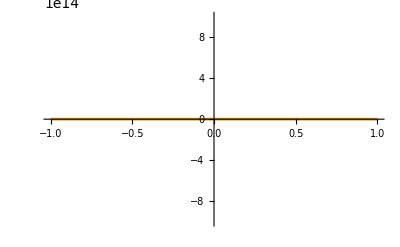

```mathematica
Plot[{fxtra[x],flt20shft[x,delt1, alph1,epsi1 ]}, {x, -1, 1}, PlotRange->Full]
```

We need to quantify how bad this is: build a table of values and then use the maximum

```mathematica
xgrid=Subdivide[-1, 1, 1999];
```

```mathematica
gridvals=Map[fxtra[#]-flt20shft[#,delt1, alph1,epsi1 ] &, xgrid];
```

```mathematica
A=Map[fxtra, xgrid];
B=Map[flt20shft[#,delt1, alph1,epsi1 ] &, xgrid];
```

```mathematica
Max[A-B]
```

0``-29.723827832295544

```mathematica
Accuracy[B[[1]]]
```

23.7572

```mathematica
Accuracy[A[[1]]]
```

-29.7238

when (1) the precision is a bit off the function build with extracted coefficients blows up near the ends of the domain. When the precision gets REALLY low then the divergence in the fcn built from coefficients gets dramatic. This shows up in the Plot fcn only but not with the map assignment -  I think what’s happening is that the plots *always* use FPP, but when I generate the values using arbitrary precision arithmetic, then the map assignment still works for some instances - see below.

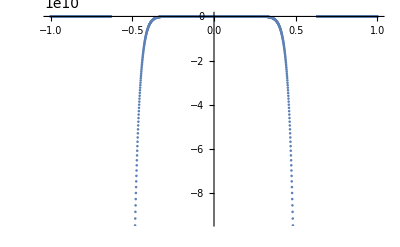

```mathematica
data=Transpose@{xgrid, A};
dataB=Transpose@{xgrid, B};
ListPlot[{data}]
```

```mathematica
diffData=Transpose@{xgrid, A-B};
```

```mathematica
ListPlot[diffData]
```

-Graphics-